(s^2 (628319.+s))/((62831.9+s) (394784.+879.646 s+s^2))

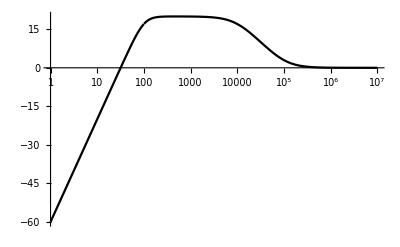

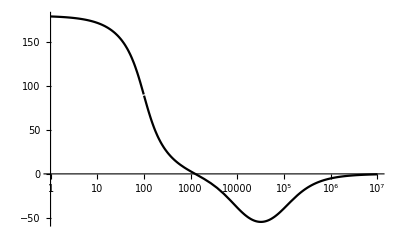

```mathematica
H[s_]:=(s^2(s+2*π*100000))/((s^2+2*0.7*2*π*100s+(2*π*100)^2)(s+2*π*10000));
Simplify[H[s]]
LogLinearPlot[20*Log10[Abs[H[ⅈ 2 π f]]],{f,1,10000000},PlotTheme->"Monochrome"]
LogLinearPlot[180/π*Arg[H[ⅈ 2 π f]],{f,1,10000000},PlotTheme->"Monochrome"]
```

```mathematica
Solve[s^2+π*280s+(2*π*100)^2==0,s]
```

{{s→20 (-7-ⅈ √51) π},{s→20 (-7+ⅈ √51) π}}

```mathematica
{{s->-439.822971502571-448.70918174495034 ⅈ},{s->-439.822971502571+448.70918174495034 ⅈ}}/.Rule->List
```

{{{s,-439.823-448.709 ⅈ}},{{s,-439.823+448.709 ⅈ}}}

```mathematica
Abs[20 (-7+ⅈ √51) π]
```

200 π

```mathematica
Abs[-439.822971502571+448.70918174495034 ⅈ]
```

628.319